## Effective Potential with metrics

```mathematica
f[r_,Ω_,γ_] = 1 - 2/r(1+Ω/r^2+(Ω γ)/r^3)^-1;
Veff[r_,L_,Ene_,ω_,Ω_,γ_] = -1 + Ene^2/f[r,Ω,γ] - ((L + ω r^2)^2)/r^2; (*ω = eB/(2mc)*)
Plot[{Veff[r,6,1,0.1,0.6,0],Veff[r,6,1,0.1,0.6,0.2],Veff[r,6,1,0.1,0.6,0.4],Veff[r,6,1,0.1,0.6,0.8]},{r,2.5,8},FrameLabel->{"r/M","V_eff(r)","E/M=1, L/M=6, ω_B = 0.1, Ω = 0.6"},Frame->True,LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],ImageSize->Large,PlotLegends->Placed[{"γ=0","γ=0.2","γ=0.4","γ=0.8"},{Scaled[{0.60,0.7}],{0,0.5}}]];

Plot[{Veff[r,6,1,0.1,0.0,0.6],Veff[r,6,1,0.1,0.2,0.6],Veff[r,6,1,0.1,0.4,0.6],Veff[r,6,1,0.1,0.8,0.6]},{r,2.5,8},FrameLabel->{"r/M","V_eff(r)","E/M=1, L/M=6, ω_B = 0.1, γ = 0.6"},Frame->True,LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],ImageSize->Large,PlotLegends->Placed[{"Ω=0","Ω=0.2","Ω=0.4","Ω=0.8"},{Scaled[{0.60,0.7}],{0,0.5}}]];

Plot[{Veff[r,6,1,-0.2,0.6,0],Veff[r,6,1,-0.2,0.6,0.2],Veff[r,6,1,-0.2,0.6,0.4],Veff[r,6,1,-0.2,0.6,0.8]},{r,2.5,8},FrameLabel->{"r/M","V_eff(r)","E/M=1, L/M=6, ω_B = -0.2, Ω = 0.6"},Frame->True,LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],ImageSize->Large,PlotLegends->Placed[{"γ=0","γ=0.2","γ=0.4","γ=0.8"},{Scaled[{0.60,0.7}],{0,0.5}}]];


Plot[{Veff[r,6,1,-0.2,0.0,0.6],Veff[r,6,1,-0.2,0.2,0.6],Veff[r,6,1,-0.2,0.4,0.6],Veff[r,6,1,-0.2,0.8,0.6]},{r,2.5,8},FrameLabel->{"r/M","V_eff(r)","E/M=1, L/M=6, ω_B = -0.2, γ = 0.6"},Frame->True,LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],ImageSize->Large,PlotLegends->Placed[{"Ω=0","Ω=0.2","Ω=0.4","Ω=0.8"},{Scaled[{0.60,0.7}],{0,0.5}}]];
```

## Angular momentum and energy

### Energy of charged particle

```mathematica
f[r_,Ω_,γ_] = 1 - 2/r(1+Ω/r^2+(Ω γ)/r^3)^-1;
Ene[ω_,Ω_,γ_,r_] = (f[r,Ω,γ] (1+r^2/16 (ω + (ω^2 + (2 D[f[r,Ω,γ],r])/(r f[r,Ω,γ]))^0.5)))^0.5;

 FindRoot[D[Ene[0,0,0,r],r]==0,{r,6}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{r→1.57088×10^37}

### Angular Momentum

```mathematica
f[r_,Ω_,γ_] = 1 - 2/r(1+Ω/r^2+(Ω γ)/r^3)^-1;
L[ω_,Ω_,γ_,r_] = 1/4(-3 ω r^2 + r^2(ω^2 + (2 D[f[r,Ω,γ],r])/(r f[r,Ω,γ]))^0.5);
Plot[L[-0.1,0.4,0.2,r]^2,{r,1.5,4}];
```

```mathematica
Solve[D[Veff[r,L,Ene,ω,Ω,γ],r]==0,Ene];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
ee = -((ⅈ √2 √(L^2-r^4 ω^2))/(r^(3/2) √((4 Ω)/(r^4 (1+Ω/r^2+(γ Ω)/r^3)^2 (1-2/(r (1+Ω/r^2+(γ Ω)/r^3)))^2)+(6 γ Ω)/(r^5 (1+Ω/r^2+(γ Ω)/r^3)^2 (1-2/(r (1+Ω/r^2+(γ Ω)/r^3)))^2)-2/(r^2 (1+Ω/r^2+(γ Ω)/r^3) (1-2/(r (1+Ω/r^2+(γ Ω)/r^3)))^2))));
Solve[-1 + ee^2/f[r,Ω,γ] - ((L + ω r^2)^2)/r^2==0,L];//Simplify
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{r→6.}

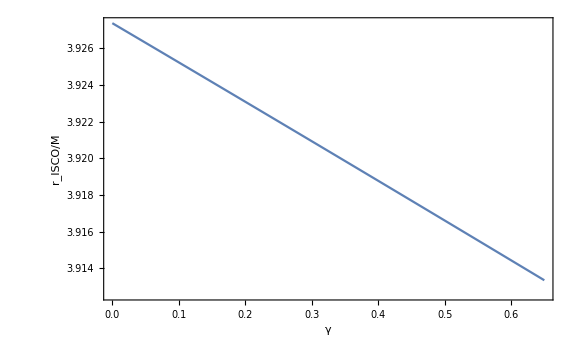

```mathematica
k[r_,Ω_,γ_,ω_]=-((r^4 (r^3-r Ω-2 γ Ω) (-ω+√(1/(r^4 (r^3-r Ω-2 γ Ω)^2)(-4 r^11 ω^2+r^12 ω^2+4 r^10 ω^2 (1+Ω)+r^9 (1+4 (-3+γ) ω^2 Ω)-2 r^2 γ Ω^3 (2+2 γ^2 ω^2-3 γ ω^2 Ω)+γ^3 Ω^3 (-2+γ ω^2 Ω)+r γ^2 Ω^3 (-5+4 γ ω^2 Ω)+2 r^6 Ω (1+ω^2 Ω (2-12 γ+3 γ^2+2 Ω))+r^7 Ω (1-12 ω^2 Ω+4 γ ω^2 (2+3 Ω))+r^8 (-3+2 ω^2 Ω (4-6 γ+3 Ω))+r^4 Ω^2 (1+ω^2 Ω^2+4 γ^2 ω^2 (1+3 Ω)-4 γ (1+3 ω^2 Ω))+r^5 Ω (6 γ-12 γ^2 ω^2 Ω+4 γ ω^2 Ω (2+3 Ω)-Ω (1+4 ω^2 Ω))+r^3 Ω^2 (-Ω+4 γ^3 ω^2 Ω-3 γ^2 (1+4 ω^2 Ω)+γ (2+4 ω^2 Ω^2))))))/(-3 r^5+r^6+2 r^4 Ω+r^3 (-1+2 γ) Ω+r^2 Ω^2+2 r γ Ω^2+γ^2 Ω^2));
FindRoot[D[k[r,0,0,0],r]==0,{r,6}]
gg = Table[γ,{γ,0,0.65,0.001}];
rr = Table[r/.FindRoot[(D[k[r,0.1,γ,0.1],r]/.{γ->gg[[i]]})==0,{r,6}],{i,1,Length[gg]}];
rrgg = Table[{gg[[i]],rr[[i]]},{i,1,Length[gg]}];
ListLinePlot[rrgg,Frame->True,FrameLabel->{"γ","r_ISCO/M"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,FontColor->Black],ImageSize->Large]
```

## ISCO radii

FindRoot::nlnum: The function value {-(23328. («1») ((0.000771605 (1.69305×10^9 Power[«2»]+«10»+108. Power[«2»] Plus[«4»]))/(216.+Times[«2»]+Times[«3»])^2-(«22» «1»«1»(«1»))/(((«1»«1»)^3)-(0.000514403 («1»))/(«1»)^2))/((23328.+2592. Ω+216. (-1.+Times[«2»]) Ω+36. Ω^2+12. γ Ω^2+γ^2 Ω^2) √((7.25594×10^8 Power[«2»]+«12»)/(216.+«1»+Times[«3»])^2))+«1»-«1»-(864. («1») (-1. ω+«21» «1»))/(23328.+2592. Ω+«1»«1»«1»+«1»+γ^2 Ω^2)} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[∂_r k[r,Ω,γ,ω]==0,{r,6.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-(23328. («1») ((0.000771605 (1.69305×10^9 Power[«2»]+«10»+108. Power[«2»] Plus[«4»]))/(216.+Times[«2»]+Times[«3»])^2-(«22» «1»«1»(«1»))/(((«1»«1»)^3)-(0.000514403 («1»))/(«1»)^2))/((23328.+2592. Ω+216. (-1.+Times[«2»]) Ω+36. Ω^2+12. γ Ω^2+γ^2 Ω^2) √((7.25594×10^8 Power[«2»]+«12»)/(216.+«1»+Times[«3»])^2))+«1»-«1»-(864. («1») (-1. ω+«21» «1»))/(23328.+2592. Ω+«1»«1»«1»+«1»+γ^2 Ω^2)} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[∂_r k[r,Ω,γ,ω]==0,{r,6.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

r/.FindRoot[∂_r k[r,Ω,γ,ω]==0,{r,6.}]

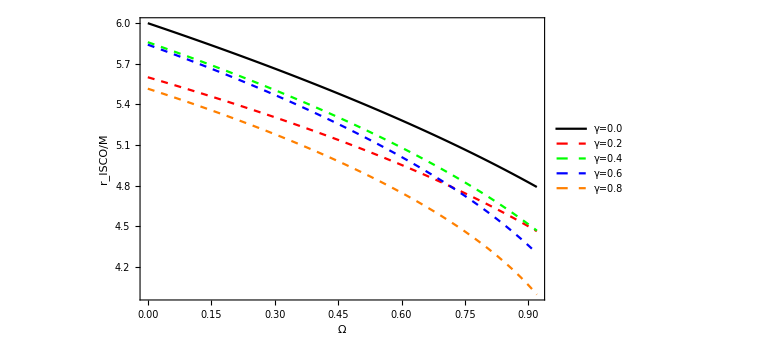

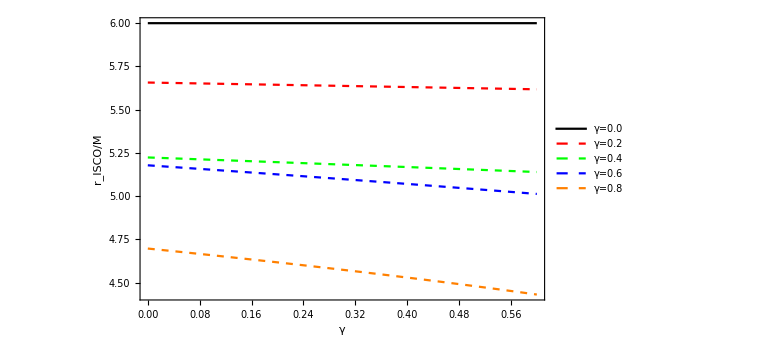

```mathematica
k[r_,Ω_,γ_,ω_]=-((r^4 (r^3-r Ω-2 γ Ω) (-ω+√(1/(r^4 (r^3-r Ω-2 γ Ω)^2)(-4 r^11 ω^2+r^12 ω^2+4 r^10 ω^2 (1+Ω)+r^9 (1+4 (-3+γ) ω^2 Ω)-2 r^2 γ Ω^3 (2+2 γ^2 ω^2-3 γ ω^2 Ω)+γ^3 Ω^3 (-2+γ ω^2 Ω)+r γ^2 Ω^3 (-5+4 γ ω^2 Ω)+2 r^6 Ω (1+ω^2 Ω (2-12 γ+3 γ^2+2 Ω))+r^7 Ω (1-12 ω^2 Ω+4 γ ω^2 (2+3 Ω))+r^8 (-3+2 ω^2 Ω (4-6 γ+3 Ω))+r^4 Ω^2 (1+ω^2 Ω^2+4 γ^2 ω^2 (1+3 Ω)-4 γ (1+3 ω^2 Ω))+r^5 Ω (6 γ-12 γ^2 ω^2 Ω+4 γ ω^2 Ω (2+3 Ω)-Ω (1+4 ω^2 Ω))+r^3 Ω^2 (-Ω+4 γ^3 ω^2 Ω-3 γ^2 (1+4 ω^2 Ω)+γ (2+4 ω^2 Ω^2))))))/(-3 r^5+r^6+2 r^4 Ω+r^3 (-1+2 γ) Ω+r^2 Ω^2+2 r γ Ω^2+γ^2 Ω^2));
rr[Ω_,γ_,ω_]=r/.FindRoot[D[k[r,Ω,γ,ω],r]==0,{r,6.}]
Plot[{rr[Ω,0,0],rr[Ω,0.2,-0.02],rr[Ω,0.4,-0.01],rr[Ω,0.6,0.01],rr[Ω,0.75,0.02]},{Ω,0.,0.92},Frame->True,FrameLabel->{"Ω","r_ISCO/M"},LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},PlotLegends->Placed[{"γ=0.0","γ=0.2","γ=0.4","γ=0.6","γ=0.8"},{Scaled[{0.60,0.7}],{-0.8,0.3}}],PlotStyle->{{Black},{Dashed,Red},{Dashed,Green},{Dashed,Blue},{Dashed, Orange}},ImageSize->Large]

Plot[{rr[0,γ,0.0],rr[0.2,γ,-0.01],rr[0.4,γ,-0.02],rr[0.6,γ,0.01],rr[0.8,γ,0.02]},{γ,0.,0.6},Frame->True,FrameLabel->{"γ","r_ISCO/M"},LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},PlotLegends->Placed[{"γ=0.0","γ=0.2","γ=0.4","γ=0.6","γ=0.8"},{Scaled[{0.60,0.7}],{-0.8,0.3}}],PlotStyle->{{Black},{Dashed,Red},{Dashed,Green},{Dashed,Blue},{Dashed, Orange}},ImageSize->Large]
```